# BEC Mean Field

## Import

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/"];
p = 0;
qc = 2000;
mr = Import["DiagMC_BEC.json", {"Data", "Impurity_Mass"} ];
```

## Recursion of P_ph

```mathematica
pMFphonit[pit_,alpha_, relm_] := NIntegrate[pMFIntegrand[pit,q,alpha,relm] , {q,0,qc}];
pMFphonit[1,1,1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in q near {q} = {0.563136}. NIntegrate obtained -157954. and 111.453 for the integral and error estimates.

-157954.

```mathematica
elast[alpha_,relm_]:=NIntegrate[ 4*Pi/(2*Pi)^3*q*q*vq2MF[q,alpha,relm]/oMEGAMF[q,relm], {q,0,qc}];
E0[alpha_,relm_]:=n0gib[alpha,relm]+eRen[alpha,relm]-elast[alpha,relm];
Ep[alpha_,relm_]:= eRen[alpha,relm]-elast[alpha,relm];
Ep[0.002, mr]
```

0.00354735

NIntegrate::nlim: q = qtemp is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

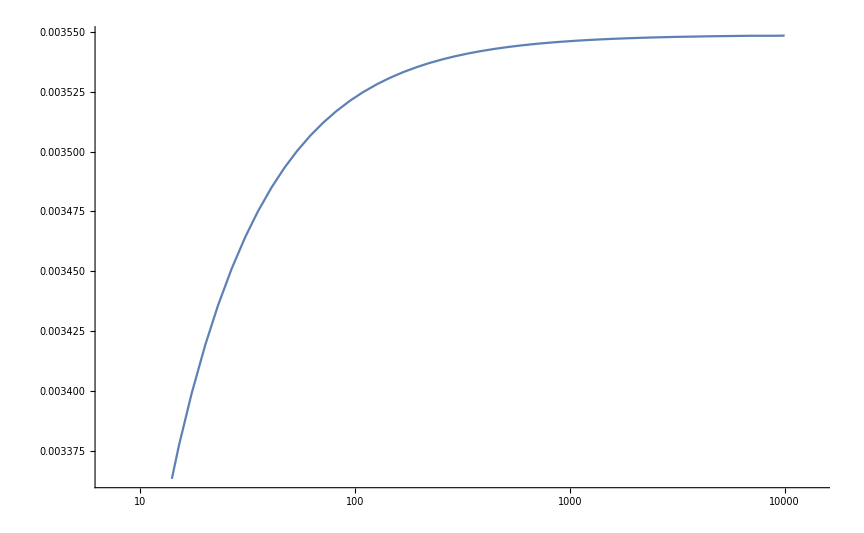

```mathematica
elast2[alpha_,relm_, qc_]:=NIntegrate[ 4*Pi/(2*Pi)^3*q*q*vq2MF[q,alpha,relm]/oMEGAMF[q,relm], {q,0,qc}];
Ep2[alpha_,relm_,qc_]:= eRenqc[alpha,relm,qc]-elast2[alpha,relm,qc];
LogLinearPlot[Ep2[0.002, mr, qtemp], {qtemp,10,10000}]
```

```mathematica
+
```

## Export

```mathematica
Epdata= Table[{alpha,Ep[alpha,mr]}, {alpha, 0.00001,0.003,0.00001}]
Export["/home/h/H.Guertner/theorie/BEC_Polaron/peter/BEC_MF_p0_small_alpha", Epdata, "Table"];
```

{{0.00001,0.0000177368},{0.00002,0.0000354735},{0.00003,0.0000532103},{0.00004,0.000070947},{0.00005,0.0000886838},{0.00006,0.000106421},{0.00007,0.000124157},{0.00008,0.000141894},{0.00009,0.000159631},{0.0001,0.000177368},{0.00011,0.000195104},{0.00012,0.000212841},{0.00013,0.000230578},{0.00014,0.000248315},{0.00015,0.000266051},{0.00016,0.000283788},{0.00017,0.000301525},{0.00018,0.000319262},{0.00019,0.000336998},{0.0002,0.000354735},{0.00021,0.000372472},{0.00022,0.000390209},{0.00023,0.000407945},{0.00024,0.000425682},{0.00025,0.000443419},{0.00026,0.000461156},{0.00027,0.000478892},{0.00028,0.000496629},{0.00029,0.000514366},{0.0003,0.000532103},{0.00031,0.000549839},{0.00032,0.000567576},{0.00033,0.000585313},{0.00034,0.00060305},{0.00035,0.000620786},{0.00036,0.000638523},{0.00037,0.00065626},{0.00038,0.000673997},{0.00039,0.000691733},{0.0004,0.00070947},{0.00041,0.000727207},{0.00042,0.000744944},{0.00043,0.00076268},{0.00044,0.000780417},{0.00045,0.000798154},{0.00046,0.000815891},{0.00047,0.000833628},{0.00048,0.000851364},{0.00049,0.000869101},{0.0005,0.000886838},{0.00051,0.000904575},{0.00052,0.000922311},{0.00053,0.000940048},{0.00054,0.000957785},{0.00055,0.000975522},{0.00056,0.000993258},{0.00057,0.001011},{0.00058,0.00102873},{0.00059,0.00104647},{0.0006,0.00106421},{0.00061,0.00108194},{0.00062,0.00109968},{0.00063,0.00111742},{0.00064,0.00113515},{0.00065,0.00115289},{0.00066,0.00117063},{0.00067,0.00118836},{0.00068,0.0012061},{0.00069,0.00122384},{0.0007,0.00124157},{0.00071,0.00125931},{0.00072,0.00127705},{0.00073,0.00129478},{0.00074,0.00131252},{0.00075,0.00133026},{0.00076,0.00134799},{0.00077,0.00136573},{0.00078,0.00138347},{0.00079,0.0014012},{0.0008,0.00141894},{0.00081,0.00143668},{0.00082,0.00145441},{0.00083,0.00147215},{0.00084,0.00148989},{0.00085,0.00150762},{0.00086,0.00152536},{0.00087,0.0015431},{0.00088,0.00156083},{0.00089,0.00157857},{0.0009,0.00159631},{0.00091,0.00161404},{0.00092,0.00163178},{0.00093,0.00164952},{0.00094,0.00166726},{0.00095,0.00168499},{0.00096,0.00170273},{0.00097,0.00172047},{0.00098,0.0017382},{0.00099,0.00175594},{0.001,0.00177368},{0.00101,0.00179141},{0.00102,0.00180915},{0.00103,0.00182689},{0.00104,0.00184462},{0.00105,0.00186236},{0.00106,0.0018801},{0.00107,0.00189783},{0.00108,0.00191557},{0.00109,0.00193331},{0.0011,0.00195104},{0.00111,0.00196878},{0.00112,0.00198652},{0.00113,0.00200425},{0.00114,0.00202199},{0.00115,0.00203973},{0.00116,0.00205746},{0.00117,0.0020752},{0.00118,0.00209294},{0.00119,0.00211067},{0.0012,0.00212841},{0.00121,0.00214615},{0.00122,0.00216388},{0.00123,0.00218162},{0.00124,0.00219936},{0.00125,0.00221709},{0.00126,0.00223483},{0.00127,0.00225257},{0.00128,0.0022703},{0.00129,0.00228804},{0.0013,0.00230578},{0.00131,0.00232351},{0.00132,0.00234125},{0.00133,0.00235899},{0.00134,0.00237673},{0.00135,0.00239446},{0.00136,0.0024122},{0.00137,0.00242994},{0.00138,0.00244767},{0.00139,0.00246541},{0.0014,0.00248315},{0.00141,0.00250088},{0.00142,0.00251862},{0.00143,0.00253636},{0.00144,0.00255409},{0.00145,0.00257183},{0.00146,0.00258957},{0.00147,0.0026073},{0.00148,0.00262504},{0.00149,0.00264278},{0.0015,0.00266051},{0.00151,0.00267825},{0.00152,0.00269599},{0.00153,0.00271372},{0.00154,0.00273146},{0.00155,0.0027492},{0.00156,0.00276693},{0.00157,0.00278467},{0.00158,0.00280241},{0.00159,0.00282014},{0.0016,0.00283788},{0.00161,0.00285562},{0.00162,0.00287335},{0.00163,0.00289109},{0.00164,0.00290883},{0.00165,0.00292656},{0.00166,0.0029443},{0.00167,0.00296204},{0.00168,0.00297977},{0.00169,0.00299751},{0.0017,0.00301525},{0.00171,0.00303299},{0.00172,0.00305072},{0.00173,0.00306846},{0.00174,0.0030862},{0.00175,0.00310393},{0.00176,0.00312167},{0.00177,0.00313941},{0.00178,0.00315714},{0.00179,0.00317488},{0.0018,0.00319262},{0.00181,0.00321035},{0.00182,0.00322809},{0.00183,0.00324583},{0.00184,0.00326356},{0.00185,0.0032813},{0.00186,0.00329904},{0.00187,0.00331677},{0.00188,0.00333451},{0.00189,0.00335225},{0.0019,0.00336998},{0.00191,0.00338772},{0.00192,0.00340546},{0.00193,0.00342319},{0.00194,0.00344093},{0.00195,0.00345867},{0.00196,0.0034764},{0.00197,0.00349414},{0.00198,0.00351188},{0.00199,0.00352961},{0.002,0.00354735},{0.00201,0.00356509},{0.00202,0.00358282},{0.00203,0.00360056},{0.00204,0.0036183},{0.00205,0.00363603},{0.00206,0.00365377},{0.00207,0.00367151},{0.00208,0.00368925},{0.00209,0.00370698},{0.0021,0.00372472},{0.00211,0.00374246},{0.00212,0.00376019},{0.00213,0.00377793},{0.00214,0.00379567},{0.00215,0.0038134},{0.00216,0.00383114},{0.00217,0.00384888},{0.00218,0.00386661},{0.00219,0.00388435},{0.0022,0.00390209},{0.00221,0.00391982},{0.00222,0.00393756},{0.00223,0.0039553},{0.00224,0.00397303},{0.00225,0.00399077},{0.00226,0.00400851},{0.00227,0.00402624},{0.00228,0.00404398},{0.00229,0.00406172},{0.0023,0.00407945},{0.00231,0.00409719},{0.00232,0.00411493},{0.00233,0.00413266},{0.00234,0.0041504},{0.00235,0.00416814},{0.00236,0.00418587},{0.00237,0.00420361},{0.00238,0.00422135},{0.00239,0.00423908},{0.0024,0.00425682},{0.00241,0.00427456},{0.00242,0.00429229},{0.00243,0.00431003},{0.00244,0.00432777},{0.00245,0.00434551},{0.00246,0.00436324},{0.00247,0.00438098},{0.00248,0.00439872},{0.00249,0.00441645},{0.0025,0.00443419},{0.00251,0.00445193},{0.00252,0.00446966},{0.00253,0.0044874},{0.00254,0.00450514},{0.00255,0.00452287},{0.00256,0.00454061},{0.00257,0.00455835},{0.00258,0.00457608},{0.00259,0.00459382},{0.0026,0.00461156},{0.00261,0.00462929},{0.00262,0.00464703},{0.00263,0.00466477},{0.00264,0.0046825},{0.00265,0.00470024},{0.00266,0.00471798},{0.00267,0.00473571},{0.00268,0.00475345},{0.00269,0.00477119},{0.0027,0.00478892},{0.00271,0.00480666},{0.00272,0.0048244},{0.00273,0.00484213},{0.00274,0.00485987},{0.00275,0.00487761},{0.00276,0.00489534},{0.00277,0.00491308},{0.00278,0.00493082},{0.00279,0.00494855},{0.0028,0.00496629},{0.00281,0.00498403},{0.00282,0.00500177},{0.00283,0.0050195},{0.00284,0.00503724},{0.00285,0.00505498},{0.00286,0.00507271},{0.00287,0.00509045},{0.00288,0.00510819},{0.00289,0.00512592},{0.0029,0.00514366},{0.00291,0.0051614},{0.00292,0.00517913},{0.00293,0.00519687},{0.00294,0.00521461},{0.00295,0.00523234},{0.00296,0.00525008},{0.00297,0.00526782},{0.00298,0.00528555},{0.00299,0.00530329},{0.003,0.00532103}}